```mathematica
piecewise[x_]:=Piecewise[{{-1,x<-1},{x,-1<x<1},{1,x>1}}]
```

```mathematica
Series[Tanh[x],{x,0,3}]
```

x-x^3/3+O[x]^4

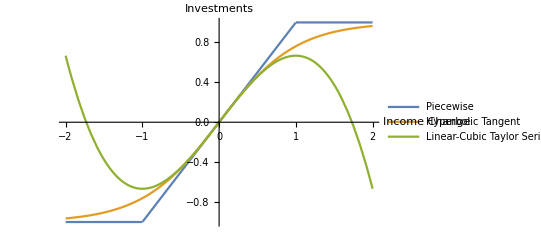

```mathematica
Plot[{piecewise[x],Tanh[x],x-x^3/3},{x,-2,2},{AxesLabel->{"Income Change","Investments"},Ticks->None,PlotLegends->Placed[{"Piecewise","Hyperbolic Tangent", "Linear-Cubic Taylor Series"},Below]}]
```

```mathematica
Export["D:\\school_work\\thesis\\presentation\\figures\\investment_curve.eps",%]
```

D:\school_work\thesis\presentation\figures\investment_curve.eps